# Análisis

## Separados por personas

People=10,100,1000
Time={20-100},{100-1000},{1000-10000}
Capacity={2-10}

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Funciones y atributos

### Variables:

exTimes es la cantidad de ejecuciones que se realizaron, las carpetas con los grafos debén estar nombradas con los números desde el 1 hasta exTimes

```mathematica
ClearVals:=Module[{},
peopleVals={10,100,1000};
capacity=Range[2,10,2];
timeVals=Range[2,10,2];
avClustering={};
avApl={};
sDClustering={};
sDApl={};exTimes=80;
];
```

### Función para importar los grafos:

Retorna una lista de largo exTimes, donde todas las redes tienen la configuración people=amountPeople, capacity=i, time=j

```mathematica
ImportGraphs[amountPeople_,i_,j_]:=
Table[Import[StringJoin["graphs/model-v3/",IntegerString[exNumber],"/","network-",IntegerString[amountPeople],"-",IntegerString[capacity[[i]]],"-",IntegerString[timeVals[[j]]*amountPeople],".g6"]],{exNumber,1,exTimes,1}];
```

### Función para calcular el promedio y la desviación estándar del clustering coefficient y del average path length:

No retorna nada, agrega un elemento a cada lista avClustering, avApl, sDClustering, sDApl. Correspondiendo al promedio y desviación estándar de las medidas de todas las redes con la configuración people=amountPeople, capacity=i, time=j

```mathematica
CalulateVals[amountPeople_,i_,j_]:=Module[{listClustering,meanClustering,sdClustering,listApl,meanApl,sdApl},
networks=ImportGraphs[amountPeople,i,j];

listClustering=Map[GlobalClusteringCoefficient,networks];
meanClustering=Mean[listClustering];
sdClustering=StandardDeviation[listClustering];

listApl=Map[MeanGraphDistance,networks];
listApl=DeleteCases[listApl,Infinity];
meanApl=Mean[listApl];
sdApl=StandardDeviation[listApl];

avClustering=Append[avClustering,meanClustering];
sDClustering=Append[sDClustering,sdClustering];
avApl=Append[avApl,meanApl];
sDApl=Append[sDApl,sdApl];
];
```

### Función para calcular todas las configuraciones tiempo - capacidad:

```mathematica
AverageVals[amountPeople_]:=Module[{},
Do[CalulateVals[amountPeople,i,j],{i,1,Length[capacity],1},{j,1,Length[timeVals],1}];
];
```

## People=10

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[10];
avClustering10=avClustering;
avApl10=avApl;
sDClustering10=sDClustering;
sDApl10=sDApl;
```

### Clustering coefficient

```mathematica
avClustering10=Partition[avClustering10,5];
```

#### capacity vs clustering coefficient

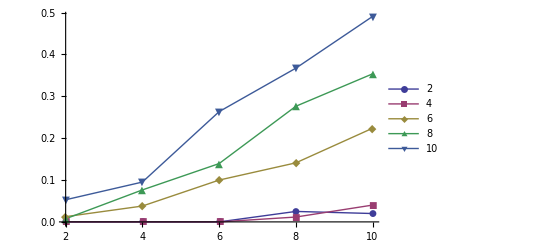
-Graphics-CapacityClustering Coefficient

```mathematica
dataPlotCl101=Table[Table[{capacity[[k]],avClustering10[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
Labeled[ListLinePlot[dataPlotCl101,PlotLegends->timeVals,PlotMarkers->Automatic],{Style["Capacity","Graphics"],Style[Rotate["Clustering Coefficient",90 Degree],"Graphics"]},{Bottom,Left}]
```

#### time vs clustering coefficient

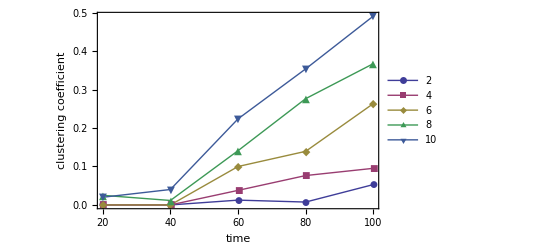

```mathematica
dataPlotCl102=Table[Table[{10timeVals[[t]],avClustering10[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotCl102,PlotLegends->capacity,Frame->{True,True,False,False},FrameLabel->{"time","clustering coefficient"},PlotMarkers->Automatic]
```

### Average path length

```mathematica
avApl10=Partition[avApl10,5];
```

#### capacity vs apl

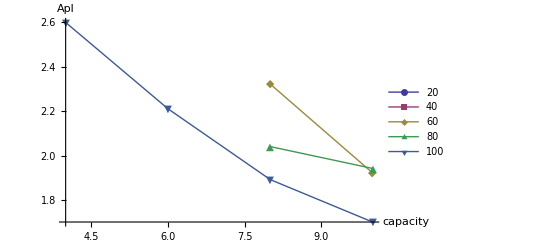

```mathematica
dataPlotApl101=Table[Table[{capacity[[k]],avApl10[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl101,PlotLegends->10timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

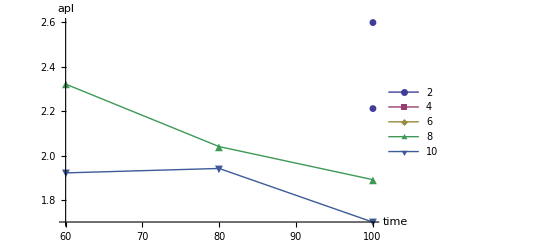

```mathematica
dataPlotApl102=Table[Table[{10timeVals[[t]],avApl10[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotApl102,PlotLegends->capacity,AxesLabel->{"time","apl"},PlotMarkers->Automatic]
```

## People=100

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[100];
avClustering100=avClustering;
avApl100=avApl;
sDClustering100=sDClustering;
sDApl100=sDApl;
```

### Clustering coefficient

```mathematica
avClustering100=Partition[avClustering100,5];
```

#### capacity vs clustering coefficient

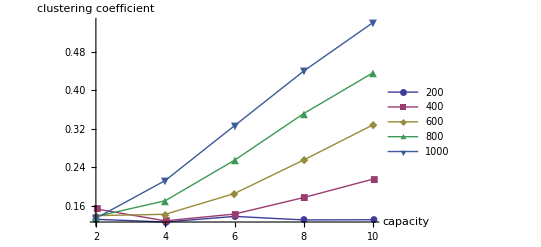

```mathematica
dataPlotCl1001=Table[Table[{capacity[[k]],avClustering100[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl1001,PlotLegends->100timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

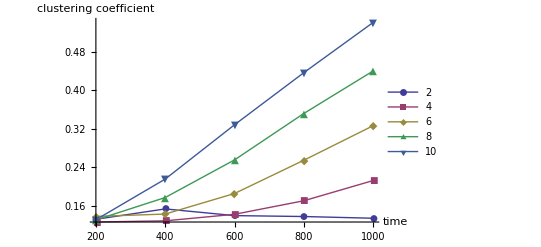

```mathematica
dataPlotCl1002=Table[Table[{100timeVals[[t]],avClustering100[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotCl1002,PlotLegends->capacity,AxesLabel->{"time","clustering coefficient"},PlotMarkers->Automatic]
```

### Average path length

```mathematica
avApl100=Partition[avApl100,5];
```

#### capacity vs apl

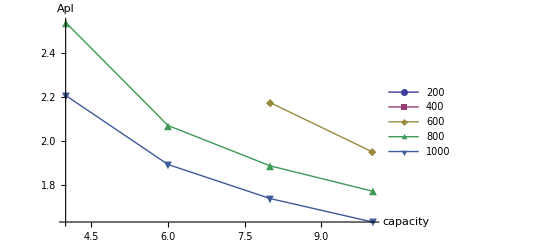

```mathematica
dataPlotApl1001=Table[Table[{capacity[[k]],avApl100[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl1001,PlotLegends->100timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

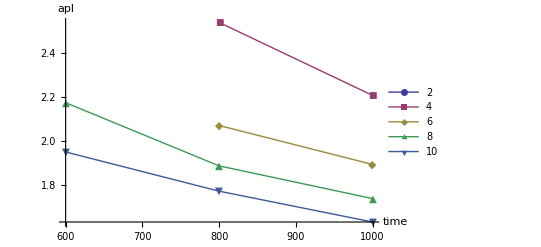

```mathematica
dataPlotApl1002=Table[Table[{100timeVals[[t]],avApl100[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotApl1002,PlotLegends->capacity,AxesLabel->{"time","apl"},PlotMarkers->Automatic]
```

## People=1000

### Sacar los valores del clustering y del apl

```mathematica
ClearVals;
AverageVals[1000];
avClustering1000=avClustering;
avApl1000=avApl;
sDClustering1000=sDClustering;
sDApl1000=sDApl;
```

### Clustering coefficient

```mathematica
avClustering1000=Partition[avClustering1000,5];
```

#### capacity vs clustering coefficient

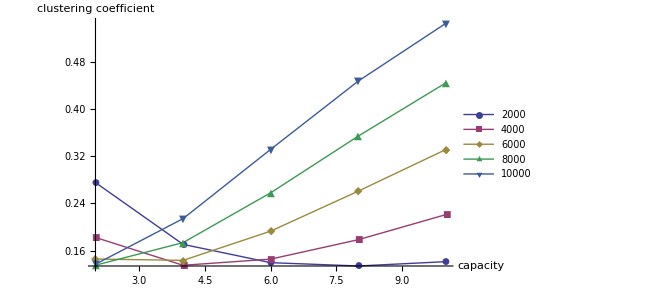

```mathematica
dataPlotCl10001=Table[Table[{capacity[[k]],avClustering1000[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl10001,PlotLegends->1000timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

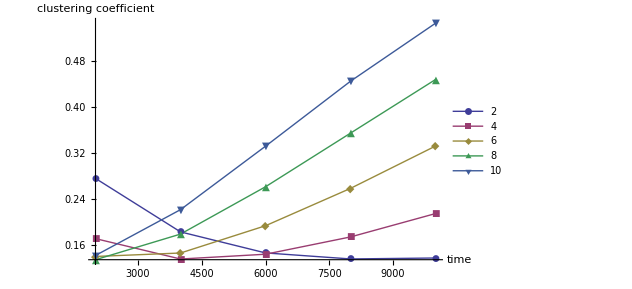

```mathematica
dataPlotCl10002=Table[Table[{1000timeVals[[t]],avClustering1000[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotCl10002,PlotLegends->capacity,AxesLabel->{"time","clustering coefficient"},PlotMarkers->Automatic]
```

### Average path length

```mathematica
avApl1000=Partition[avApl1000,5];
```

#### capacity vs apl

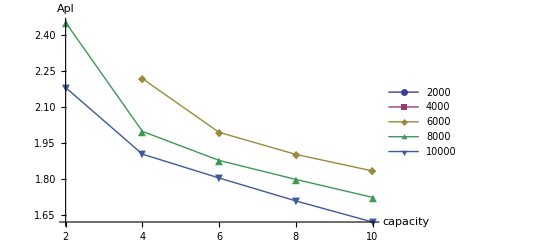

```mathematica
dataPlotApl10001=Table[Table[{capacity[[k]],avApl1000[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotApl10001,PlotLegends->1000timeVals,AxesLabel->{"capacity","Apl"},PlotMarkers->Automatic]
```

#### time vs apl

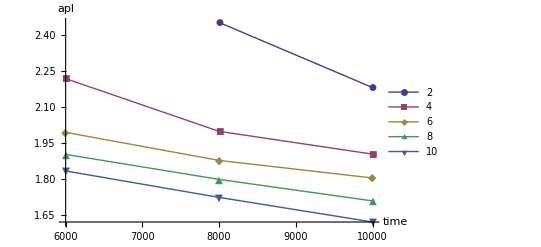

```mathematica
dataPlotApl10002=Table[Table[{1000timeVals[[t]],avApl1000[[k,t]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotApl10002,PlotLegends->capacity,AxesLabel->{"time","apl"},PlotMarkers->Automatic]
```